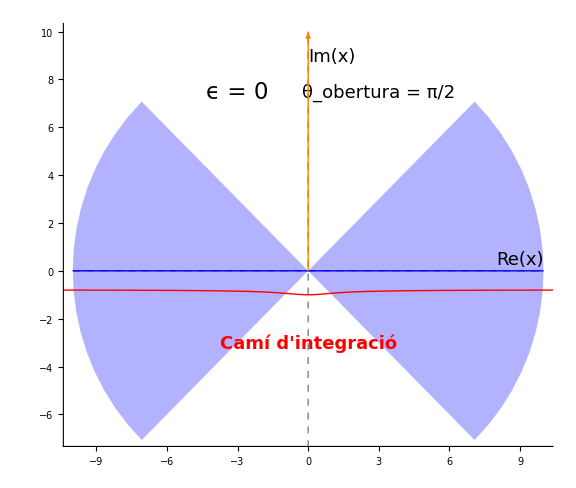

```mathematica
(*Definicions*)
centroDerecha[eps_]:=-(Pi*eps)/(8+2*eps);
centroIzquierda[eps_]:=-Pi+(Pi*eps)/(8+2*eps);
amplitud[eps_]:=(2*Pi)/(4+eps);
xParam[t_,eps_]:=-I*(1/(1-t^2))*Exp[(2*Pi*I*t)/(4+eps)];
eps=0; 

Module[{cDer,cIzq,amp,radio=10},cDer=centroDerecha[eps];
cIzq=centroIzquierda[eps];
amp=amplitud[eps];
Graphics[{(*eixos i fons*){GrayLevel[0.9],PointSize[0],Point[{0,0}]},{Gray,Dashed,Line[{{-radio,0},{radio,0}}],Line[{{0,-radio},{0,radio}}]},(*sector dret*){Opacity[0.3],Blue,Disk[{0,0},radio,{cDer-amp/2,cDer+amp/2}]},{Blue,Thick,Line[{{0,0},radio {Cos[cDer],Sin[cDer]}}]},(*sector esq.*){Opacity[0.3],Blue,Disk[{0,0},radio,{cIzq-amp/2,cIzq+amp/2}]},{Blue,Thick,Line[{{0,0},radio {Cos[cIzq],Sin[cIzq]}}]},(* x(t)*){Red,Thick,Line[Table[{Re[xParam[t,eps]],Im[xParam[t,eps]]},{t,-0.97,0.97,0.005}]]},(*etiquetes*){Black,Text[Style["Re(x)",18],{radio-1,0.5}]},{Black,Text[Style["Im(x)",18],{1,radio-1}]},{Red,Text[Style["Camí d'integració",18,Bold],{0,-0.3*radio}]},{Orange,Thick,Arrowheads[Medium],Arrow[{{0,0},{0,radio}}]},{Black,Text[Style[Row[{"θ_obertura = ",NumberForm[amp,{5,3}]}],18,Background->White],{3,radio-2.5}]},{Black,Text[Style[Row[{"ϵ = ",eps}],23,Background->White],{-radio+7,radio-2.5}]}
},PlotRange->{{-radio,radio},{-0.7*radio,radio}},Axes->True,ImageSize->Large]]
```